## t vs C Plot

The txt files “cosT” and”” to import are from “coeficientes fourier for Fig 3a.nb”.
The txt file and the notebook can be found in the same folder.

### Data Import: (*change it to the local directory where the cos.txt and sinT.txt file is*)

```mathematica
directorio="(*your directory here*)\\";
```

#### We import the data:

```mathematica
aT3=Import[StringJoin[directorio,"cosT.txt"],"TSV"];
bT3=Import[StringJoin[directorio,"sinT.txt"],"TSV"];

aT3=ToExpression[aT3];
bT3=ToExpression[bT3];
```

Where:

aT3[[1]]               b=1.76921  n=-2            
aT3[[2]]               b=1.76921  n=2
aT3[[3]]               b=1.82272  n=-3
aT3[[4]]               b=1.82272  n=3
aT3[[5]]               b=1.82272  n=-4
aT3[[6]]               b=1.82272  n=4
aT3[[7]]               b=1.903  n=-4
aT3[[8]]               b=1.903  n=4
aT3[[9]]               b=1.903  n=-5
aT3[[10]]             b=1.903  n=5
aT3[[11]]             b=1.903  n=-4 continuación

#### Function to calculate Sqrt[a^2+b^2]

```mathematica
sum[x_(*sin value*),y_(*cos value*)]:=Module[{},n3=Table[Sqrt[(x⟦i,2;;⟧)^2+(y⟦i,2;;⟧)^2],{i,1,Length[x]}]]
```

#### Function to find the position of the biggest Fourier Coefficient

```mathematica
max[x_(*sin value*),y_(*cos value*)]:=Module[{},n3=Table[Sqrt[(x⟦i,2;;⟧)^2+(y⟦i,2;;⟧)^2],{i,1,Length[x]}];mx3=Table[Position[n3⟦i⟧,Max[Abs[n3⟦i⟧⟦2;;⟧]]],{i,1,Length[x]}]]
```

#### Function to find the value of the biggest Fourier Coefficient

```mathematica
listavaloresmaximos[x_(*sin value*),y_(*cos value*)]:=Module[{},n3=Table[Sqrt[(x⟦i,2;;⟧)^2+(y⟦i,2;;⟧)^2],{i,1,Length[x]}];mx3=Table[Position[n3[[i]],Max[Abs[n3[[i]][[2;;]]]]],{i,1,Length[x]}];gra3=Table[n3[[i,mx3[[i,1]]]],{i,1,Length[x]}]]
```

List of the biggest Fourier Coefficients

```mathematica
abT=Table[Flatten[listavaloresmaximos[aT3[[i]],bT3[[i]]]],{i,1,11}];
```

#### Function to plot the list of the biggest Fourier Coefficients

```mathematica
Grafica[x_(*sin value*),y_(*cos value*)]:=Module[{},n3=Table[Sqrt[(x⟦i,2;;⟧)^2+(y⟦i,2;;⟧)^2],{i,1,Length[x]}];mx3=Table[Position[n3[[i]],Max[Abs[n3[[i]][[2;;]]]]],{i,1,Length[x]}];gra3=Table[n3[[i,mx3[[i,1]]]],{i,1,Length[x]}];ListLogLinearPlot[{Flatten[gra3]},Joined->True,PlotRange->All]
]
```

### Time step (to adjust the scale):

```mathematica
tn3=Table[i,{i,0,3223.4/10000*3000,100*0.32234}];
tn5=Table[i,{i,0,1312.4/10000*2000,5*0.13124}];
tn7=Table[i,{i,0,694.62/10000*2000,5*0.06947}];
tn74n=Table[i,{i,0,1000,.5}];
tn74n2=Table[i,{i,800,2000,.2*100}];
tn74n1=Table[i,{i,0,780,.2*100}];
t={tn3,tn3,tn5,tn5, tn5,tn5,tn74n,tn7,tn7,tn7,tn74n1};
```

### Plots:

#### We can plot them individually :

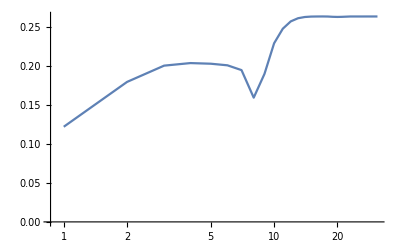
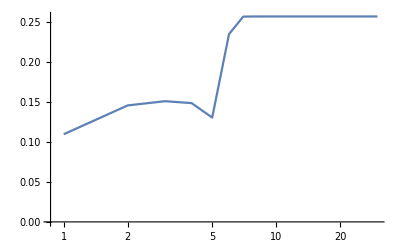
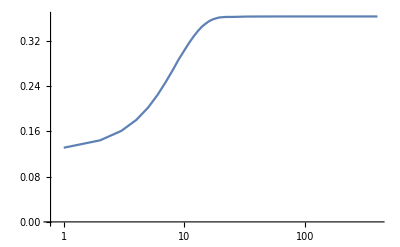
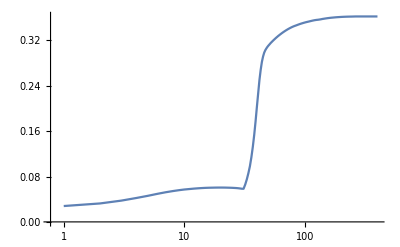
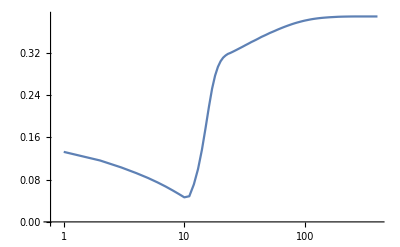
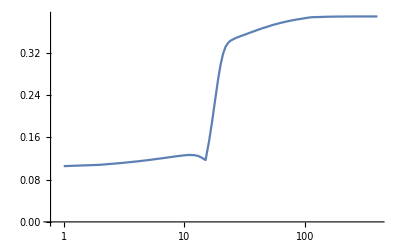
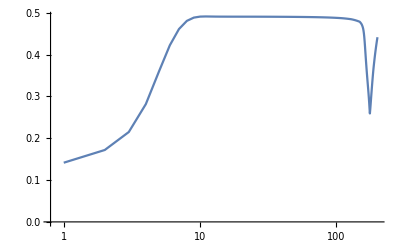
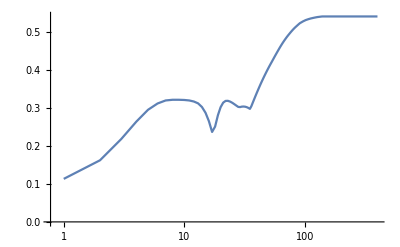

```mathematica
Table[Grafica[aT3⟦i⟧,bT3⟦i⟧ ],{i,1,11}]
```

#### Or together:

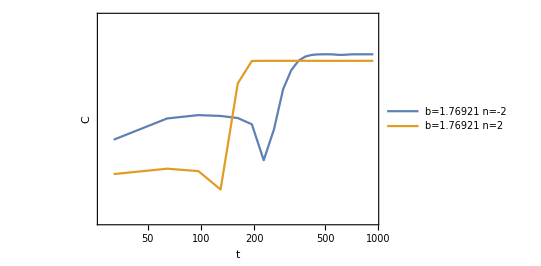

```mathematica
C3=ListLogLinearPlot[{Transpose[{t[[1]][[;;30]],abT[[1]][[;;30]]}],Transpose[{t[[2]][[1;;30]],abT[[2]]}]},PlotRange->{.1,.3},PlotLegends->{" b=1.76921 n=-2","b=1.76921 n=2"},Joined->True,AspectRatio->1/1.5, Frame->True, FrameTicks->{{None,{.1,.2,.3}},{None,{50,100,200,400,800}}}, ImageSize->400, FrameTicksStyle->Directive[Gray,24], FrameLabel->{Text[Style["t",28,Italic, Black]],Text[Style["C",28,Italic, Black]]}]
```

### We are interested in the plot for b=1.903, this mean the index 7,8,9 and 10 of our data.

```mathematica
list1=Transpose[{Flatten[{t⟦7⟧⟦;;175⟧*1.8,t⟦11⟧⟦10;;⟧}],Flatten[{abT⟦7⟧⟦;;175⟧,abT⟦11⟧⟦10;;⟧-.16}]}];list2=Transpose[{Flatten[{{t⟦8⟧},{800}}],Flatten[{abT⟦8⟧,Last[abT⟦8⟧]}]}];list3=Transpose[{Flatten[{{t⟦9⟧},{800}}],Flatten[{abT⟦9⟧,Last[abT⟦9⟧]}]}];list4=Transpose[{Flatten[{{t⟦10⟧},{800}}],Flatten[{abT⟦10⟧,Last[abT⟦10⟧]}]}];
```

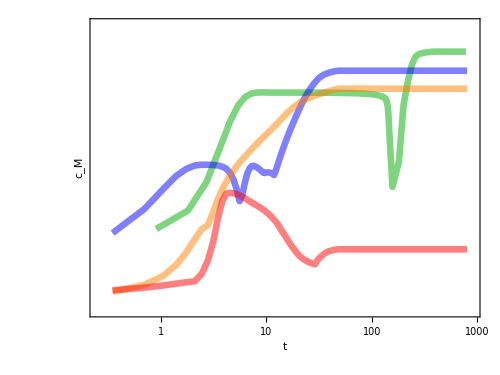

```mathematica
C7b=ListLogLinearPlot[{list1,list2,list3,list4},PlotRange->{{0.25,900},{-0.02,.65}},Joined->True,AspectRatio->0.75, Frame->True, FrameTicks->{{None,{0,.2,.4,.6}},{None,{0.5,5,50,500}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["t",38,Italic, Black]],Text[Style["c_M",38,Italic, Black]]},PlotStyle->{{Opacity[0.5,Darker[Green]],Thickness[0.0095]},{Opacity[0.5,Blue],Thickness[0.0095]},{Opacity[0.5,Orange],Thickness[0.0095]},{Opacity[0.5,Red],Thickness[0.0095]}}]
```

```mathematica
(*PlotLegends->{"b=1.903 n=-4", "b=1.903 n=4","b=1.903 n=-5", "b=1.903 n=5"},*)
```

```mathematica
Export["fig3v1p0b.png",C7b,ImageResolution->250]
```

fig3v1p0b.png